# Lorentz System

The general ODE is

```mathematica
Lorentz[{σ_,ρ_,β_}][{x_,y_,z_}]:= {σ (y-x), x( ρ-z) - y,x y - β z}
DLorentz[{σ_,ρ_,β_}][{x_,y_,z_}]:= {{-σ,σ,0},{-z+ρ,-1,-x},{y,x,-β}}
```

## Standard Parameters

Typical chaotic behavior below occurs for  {σ,ρ,β}={10,28,8/3}.

```mathematica
σρβ={10.0,28, 8/3};
f[{x_,y_,z_}]:= Lorentz[σρβ][{x,y,z}]
df[{x_,y_,z_}]:= DLorentz[σρβ][{x,y,z}]

{p0, TMax}={{1,1,1},23};
pSol=NDSolveValue[ {p'[t]==f[p[t]], p[0]==p0},p,{t,0, TMax}];
WingPic=ParametricPlot3D[pSol[t],{t, 0, TMax},
PlotPoints->1000, PlotStyle->Thin,
AxesLabel->{"x","y","z"}]
```

-Graphics3D-

### Equilibrium Points

We would like to know where (and what) the equilibrium points are. As shown below there are three: one at the origin and the other two in the middle of the wings.

```mathematica
{x,y,z}/.Solve[  {σ (y-x), x( ρ-z) - y,x y - β z}=={0.,0,0}, {x,y,z}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{0.,0.,0.},{-1. √β √(-1.+ρ),-1. √β √(-1.+ρ),-1.+ρ},{√β √(-1.+ρ),√β √(-1.+ρ),-1.+ρ}}

This defines the + wing equilibrium point.

```mathematica
WingEq[{σ_,ρ_,β_}]:= {√β √(ρ-1),√β √(ρ-1),ρ-1}
```

Lets chek they are where we think they are!

```mathematica
wEq = WingEq[σρβ];
Show[WingPic, Graphics3D[{PointSize[0.025],
{Red,Point[wEq]},
{Orange,Point[{-1,-1,1}wEq]},
{Blue,Point[{0,0,0}]}
}]]
```

-Graphics3D-

### Behavior Near Equilibrium Points

To characterize the equilibrium points we need to know the nature of the linearization: we need the eigenvalue of the derivatives!  We only need one wing since we know the other is a “twin”.

```mathematica
Map[Eigenvalues[df[#]]&,{{0.0,0,0},wEq}]
```

{{-22.8277,11.8277,-2.66667},{-13.8546+0. ⅈ,0.0939556+10.1945 ⅈ,0.0939556-10.1945 ⅈ}}

The origin sucks in fast along two directions (a plane of sucking in) and spits out along one direction.

The “in” directions are the eigenvectors associated with the negative eigenvalues.

The “out” direction is the  eigenvector associated with the positive eigenvalue.

The wings suck in fast along one direction and spin out slowly in a plane.

The “in” direction is the eigenvector associated with the negative eigenvalue.

The “spin-out” plane is the span of the real and complex parts of the complex eigenvectors associated with the complex eigenvalues.

```mathematica
{OriginIn1, OriginOut2,OriginIn3}=Eigenvectors[df[{0.0,0,0}]]
{WingIn1,WingSpin2,WingSpin3}=Chop[Eigenvectors[df[wEq]]]
```

{{-0.614817,0.78867,0.},{-0.416504,-0.909134,0.},{0.,0.,1.}}

{{0.855665,-0.329823,-0.398816},{-0.266119-0.29501 ⅈ,0.0321286-0.569077 ⅈ,-0.719214},{-0.266119+0.29501 ⅈ,0.0321286+0.569077 ⅈ,-0.719214}}

These unit vectors need to be made bigger to see them on the pic!

```mathematica
Show[WingPic, Graphics3D[{PointSize[0.025],
{Red,Point[wEq]},{Orange,Point[{-1,-1,1}wEq]},{Blue,Point[{0,0,0}]},
{Cyan, Arrow[{{0,0,0}+10 OriginIn1,{0,0,0}}],Arrow[{{0,0,0}+10 OriginIn3,{0,0,0}}]},
{Green,Arrow[{{0,0,0},{0,0,0}-10 OriginOut2}]},
{Red, Arrow[{wEq,wEq+10 Re[WingSpin2]}],Arrow[{wEq,wEq+10 Im[WingSpin2]}]},
{Black, Arrow[{wEq+10 WingIn1,wEq}]}
}]]
```

-Graphics3D-

The other wing is the similar. The real part of the complex conjugate pair α±I β gives how fast the radius grows ⅇ^(α t)near the wing equilibrium.  The imaginary part gives the rotation “speed” cos(β t).   The negative real eigenvalue gives how fast anything of the wing gets sucked into the wing

```mathematica
{λIn1,λSpin2,λSpin3}=Eigenvalues[df[wEq]]
{α,β}=ReIm[λSpin2]
{p0, TMax}={wEq+5 WingIn1,32};
pSol=NDSolveValue[ {p'[t]==f[p[t]], p[0]==p0},p,{t,0, TMax}];
wComp={1,1,0}; tComp =1; 
TabView[{
"3D"->ParametricPlot3D[pSol[t],{t, 0, TMax},
PlotPoints->1000, PlotStyle->Thin,
AxesLabel->{"x","y","z"}],
"Suck In"->LogLinearPlot[{(pSol[t]-wEq).WingIn1,(pSol[0]-wEq).WingIn1 E^(λIn1 t)},{t,0, 10},
PlotRange->All,GridLines->Automatic,
PlotLegends->{"perp","theory"},
AxesLabel->{"t","perp"}],
"Spin Out"->Plot[{
{pSol[t]-wEq}.wComp, 
Cos[β( t-tComp)]*{pSol[tComp]-wEq}.wComp E^(α(t-tComp))
},{t,0, TMax},
PlotLegends->{"p.w","theory"},
PlotRange->All,GridLines->Automatic,
AxesLabel->{"t",""}]}]
```

{-13.8546+0. ⅈ,0.0939556+10.1945 ⅈ,0.0939556-10.1945 ⅈ}

{0.0939556,10.1945}

123

### Poincare Sections

We decided that we would put a vertical plane in through the origin and rotate it.

```mathematica
{p0, TMax}={{1,1,1},23};
pSol=NDSolveValue[ {p'[t]==f[p[t]], p[0]==p0},p,{t,0, TMax}];
WingPic=ParametricPlot3D[pSol[t],{t, 0, TMax},
PlotPoints->1000, PlotStyle->Thin,
AxesLabel->{"x","y","z"}];
θ=π/2; 
{xx,yy}=20 {Cos[θ],Sin[θ]};
Show[
WingPic,
Graphics3D[{Opacity[0.5],Green,Polygon[{
{-xx,-yy,0},
{xx,yy,0},
{xx,yy,50},
{-xx,-yy,50}}]}],
PlotRange->{{-20,20},{-20,20},{0,50}}
]
```

-Graphics3D-

I have several ways to build the section.  I can catch and export points from the ODE solver.

```mathematica
{p0, TMax}={{1,1,1},123};
θ=π/4;
{pSol,poincarePoints}=Reap[
NDSolveValue[ {p'[t]==f[p[t]], p[0]==p0},p,{t,0, TMax},
Method->{"EventLocator","Event"->p[t].{Sin[θ],-Cos[θ],0},"Direction"->1, "EventAction":>Sow[p[t]]}]
];
 {xx,yy}=30 {Cos[θ],Sin[θ]};
Show[
ParametricPlot3D[pSol[t],{t, 0, TMax},
PlotPoints->1000, PlotStyle->Thin,
AxesLabel->{"x","y","z"}],
Graphics3D[{
Map[Point,poincarePoints],
{Opacity[0.5],Green,Polygon[{
{-xx,-yy,0},
{xx,yy,0},
{xx,yy,50},
{-xx,-yy,50}}]}}],
PlotRange->{{-20,20},{-20,20},{0,50}}
]
```

-Graphics3D-

Each θ needs a new ODE solve.  Most folks have been computing the solution of the ODE once and then approximating the poincare section points afterwards.  The following rescues the {x,y,z} data out of the interpolating function.  You can see that the steps are smallish but far from tiny! We are going to have some fuzziness in our data if/when we go this root.

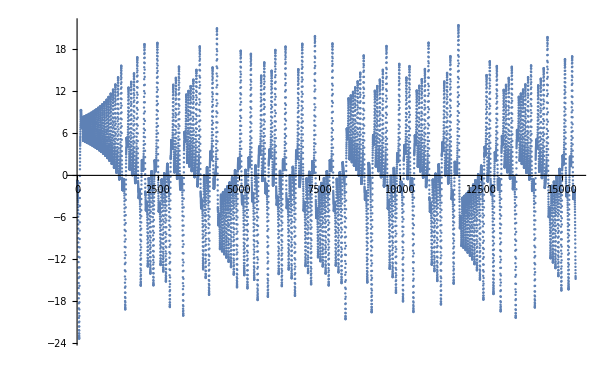

```mathematica
xyzVals=pSol⟦4,All,1⟧;
(*Graphics3D[Map[Point,xyzVals]]*)
θ=0.2;
normalVec={Sin[θ],-Cos[θ],0};
ListPlot[Map[normalVec.#&,xyzVals]]
```

Our target is to find the crossing points! We need either the +→- or the -→+ ones!  Most folks I have seen have been scanning through the entries (nothing wrong with that it is just inherently very serial). Here is a parallel way to do the same thing.
1) Detect the changes

```mathematica
xyzVals=pSol⟦4,All,1⟧;
(*Graphics3D[Map[Point,xyzVals]];*)
θ=0.2;
normalVec={Sin[θ],-Cos[θ],0};
Hmm=Position[Partition[Map[Sign[normalVec.#]&,xyzVals],2],{1,-1}]
```

{{649},{1054},{1255},{1545},{1589},{1816},{2175},{2543},{2614},{3026},{3079},{3146},{3236},{3295},{3437},{3691},{3871},{3962},{4070},{4446},{4799},{4911},{5112},{5155},{5351},{5394},{5449},{5549},{5606},{5738},{6210},{6263},{6397},{6739},{7190},{7232},{7473},{7671}}

2) Fill in the gap. Interpolation is better than other things!

```mathematica
i=649;
{w1,w2}=Map[normalVec.#&,xyzVals⟦2*i-1;;2*i⟧];
xyzMean=(xyzVals⟦2*i-1⟧+xyzVals⟦2*i⟧)/2;
w= w2/(w2-w1);
xyzInterpolated=w*xyzVals⟦2*i-1⟧+(1-w)xyzVals⟦2*i⟧;
Map[normalVec.#&,{xyzVals⟦2*i-1⟧,xyzVals⟦2*i⟧,xyzMean,xyzInterpolated}]
```

{0.0676181,-0.0554714,0.00607336,2.22045×10^-16}